# Mathematica: The Basics

## Physics 7321

## Rich Text Editor

Mathematica is a “rich text editor” similar to the .ipynb files of python and .mlx files of MATLAB, meaning that

plots and graphics will appear inline

special characters can be inserted using latex type commands

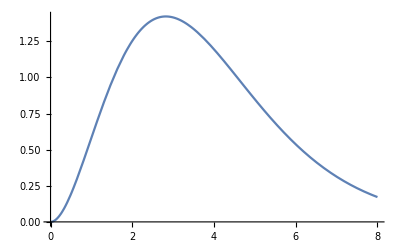

π^4/15

```mathematica
Plot[x^3/(Exp[x]-1),{x,0,8}]
Integrate[x^3/(Exp[x]-1),{x,0,∞}]
```

```mathematica
∫x^3/(Exp[x]-1)ⅆx
```

```mathematica
-x^4/4+x^3 Log[1-ⅇ^x]+3 x^2 PolyLog[2,ⅇ^x]-6 x PolyLog[3,ⅇ^x]+6 PolyLog[4,ⅇ^x]
```

## A notebook is made from “cells”

Everything in Mathematica from text to input is contained within cells.

Press Shift+Enter to evaluate cell

Much of the formatting will apply to the entire cell

Use Ctrl+Shift+d to divide cell

## Defining Functions makes Syntax even easier

### Define Function

Putting a ‘:’ before the equal sign esures that Mathematica updates the function every time it is called

```mathematica
a=2;
f[x_]:= (a*x^3)/(Exp[x]-1);
g[x_] = (a*x^3)/(Exp[x]-1);
```

```mathematica
f[2]-g[2]
a=4;
f[2]-g[2]
```

Your functions can contain as many variables as you want

## Manipulate - What a great feature

There are times when you’d like to explore a function and the dependence of different parameters on the output. 
Well, use Manipulate:

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,300,1}]
```

```mathematica
Manipulate[Plot[A*Sin[n*x]+B*Cos[n*x],{x,0,2 Pi}],{n,1,20},{A,1,5},{B,0,5}]
```